# Homework week 1 - Paolo Zinesi

## Solution of the Consumer Resource Model (CRM) with abiotic resources, displaying both the (full) numerical solution and the solution obtained using the Quasi-Static Approximation (QSA).

```mathematica
γ=0.8;
ks=10;
c=0.01;
d=0.1;
```

```mathematica
Nstar = 1/(c*ks+(d/γ)) (* large times limit of N[t] *);
Rstar = 1/(c*Nstar)-ks (* large times limit of R[t] *);
```

```mathematica
Nstar
```

4.44444

```mathematica
Rstar
```

12.5

It is important to check if the value of R* (Rstar) is greater than zero

```mathematica
Rstar >0
```

True

```mathematica
N0 = 10;
R0 = 50;
NQSA =((N0-Nstar)*Exp[-(γ/Nstar)*#]+Nstar)&;
```

```mathematica
sol = NDSolve[{n'[t]==(γ*c*R[t]-d)*n[t], R'[t]==(R[t]/(ks+R[t])) -c*R[t]*n[t], R[0]==R0, n[0]==N0},{n[t],R[t]},{t,0,1000}]
```

{{n[t]→InterpolatingFunction[…][t],R[t]→InterpolatingFunction[…][t]}}

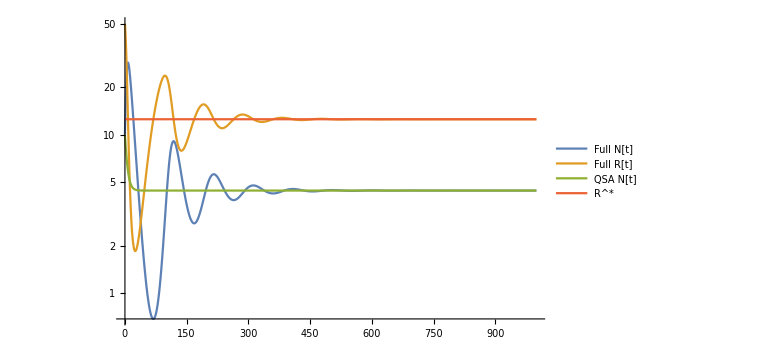

```mathematica
Plot[{Evaluate[{n[t],R[t]}/.Association[sol]],NQSA[t], Rstar},{t,0,1000},PlotRange->Automatic, PlotLegends->{"Full N[t]","Full R[t]","QSA N[t]", Superscript["R","*"]}, ScalingFunctions->"Log", ImageSize->Large]
```

From the plots above it is possible to see that the QSA gives a good solution in the limit of long times. Both the numerical solutions of N[t] and of R[t] approach the values denoted as N* and R* in the cells above. While the full numerical solutions oscillates very much, the QSA solution of N[t] approaches N* exponentially and without oscillations since in QSA the time variation of the resources R[t] is neglected.